# NN knocout Inverse Kinematic

```mathematica
c=299792458;
mp=938.27203;
mn=939.56536;
md=1875.612793;
m10B = 9326.99;
m11B=10255.1;
m12B =11191.3;
m12C=11178;
massList={mp->"π",mn->"μ",md->"D",m10B->"10B",m11B->"11B",m12B->"12B",m12C->"12C"};
(* parameters *)
(* Sp = seperation energy*)
(* ksc, θsc, ϕsc = scattered proton *)
(* kNN, θNN, ϕNN = NN pair inside nucleus *)
(*, BNN = blinding enegry of NN pair *)
(* kN, θN, ϕN = internal motion of the NN pair*)
```

### Titled Lorentz Transfrom and Rotation

The Lorentz Tranform on aribtary direction is well discrpted in Goldstien P .281

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
(* rotation *)
R[ϕNN_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[ϕNN].Ry[θ].Rz[ϕ];
```

### 4 vector contruction

```mathematica
PmTθ[m_, T_, θ_, ϕ_]:={m+T, √(2m T+T^2) Cos[ϕ]Sin[θ], √(2m T+T^2) Sin[ϕ]Sin[θ], √(2m T+T^2)Cos[θ]};
Pmkθ[m_, k_, θ_, ϕ_]:={√(m^2+k^2), k Cos[ϕ]Sin[θ], k Sin[ϕ]Sin[θ], k Cos[θ]};
PNNkθB[kNN_, θNN_,ϕNN_,BNN_]:={√(kNN^2+(mp+mn)^2-BNN), kNN Cos[ϕNN]Sin[θNN], kNN Sin[ϕNN]Sin[θNN], kNN Cos[θNN]}
```

### Convertor

```mathematica
Mass[E_,k_]:=√(E^2-k^2);
Momentum[A_]:=√(A[[2]]^2+A[[3]]^2+A[[4]]^2);
k2T[k_,m_]:=√(m^2+k^2)-m;
KE[A_,m_]:=A[[1]]-m
T2k[T_,m_]:=√(2m T+T^2);
Angle[A_]:=If[A[[2]]==0 && A[[3]]==0,{0,0},{ArcTan[A[[4]],√(A[[2]]^2+A[[3]]^2)],ArcTan[A[[2]],A[[3]]]}];
β[A_]:=Momentum[A]/A[[1]]
(* angle between 2 vector*)
ΔAngle[A_,B_]:=ArcCos[(A[[2]]B[[2]]+A[[3]]B[[3]]+A[[4]]B[[4]])/(Momentum[A]Momentum[B])];
(* Display DisVector *)
DisVector[A_,name_]:={name,A[[1]],A[[2]],A[[3]],A[[4]]}
DisEnergy[A_,m_,name_]:={name,A[[1]]-m,Momentum[A],Angle[A][[1]] 180/π,Angle[A][[2]] 180/π}
```

## Reaction

```mathematica
(* in nucleus frame *)
(* change to CM frame of proton and NN *)
knockout[k_,θk_,ϕk_,θc_,ϕc_,S_,kNN_,θNN_, ϕNN_, SNN_,mTar_,mi_,mknockout_,m1_, m2_,TiL_]:={
PI=PmTθ[mi, TiL, 0, 0];
Pn=Pmkθ[mTar-√((mTar-mknockout+S)^2+k^2),k,θk,ϕk]; (* fake 4 vector, for construct the CM frame of a-X*)
Pc=(PI+Pn)/2;
βPc=β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame of a X *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
PIc=PI.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θIc,ϕIc}=Angle[PIc];
Etotal=√(1-βPc^2)(PI[[1]]+Pn[[1]]); (* total energy of E1c and E2c *)
k1c=1/(2 Etotal)(√((Etotal-mi-mknockout)(Etotal+mi-mknockout) (Etotal-mi+mknockout) (Etotal+mi+mknockout)));
P1c={√(mi^2+k1c^2),k1c Sin[θIc+θc]Cos[ϕIc],k1c Sin[θIc+θc]Sin[ϕIc], k1c Cos[θIc+θc]}.R[ϕc,θIc,ϕIc];
P2c={√(mknockout^2+k1c^2) ,k1c Sin[θIc+θc+π]Cos[ϕIc],k1c Sin[θIc+θc+π]Sin[ϕIc], k1c Cos[θIc+θc+π]}.R[ϕc,θIc,ϕIc];
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
β2=β[P2];
{θ2,ϕ2}=Angle[P2];
E2tot = √((m1+m2)^2+kNN^2)-SNN;
k2aNN = 1/(2 E2tot)(√((E2tot-m1-m2)(E2tot+m1-m2) (E2tot-m1+m2) (E2tot+m1+m2)));
P2aNN = {√(m1^2+k2aNN^2),k2aNN Sin[θNN+θ2]Cos[ϕ2],k2aNN Sin[θNN+θ2]Sin[ϕ2], k2aNN Cos[θNN+θ2]}.R[ϕNN,θ2,ϕ2];
P2bNN =  {√(m2^2+k2aNN^2),-k2aNN Sin[θNN+θ2]Cos[ϕ2],-k2aNN Sin[θNN+θ2]Sin[ϕ2], -k2aNN Cos[θNN+θ2]}.R[ϕNN,θ2,ϕ2];
P2a = P2aNN.L[β2,θ2,ϕ2];
P2b = P2bNN.L[β2,θ2,ϕ2];
βI=β[PI];
PIL = PI.L[-βI,0,0];
P1L=P1.L[-βI,0,0];
P2L=P2.L[-βI,0,0];
P2aL=P2a.L[-βI,0,0];
P2bL=P2b.L[-βI,0,0];
(* output *)
(*PIL, P1L, P2L,P2aL,P2bL,*)
180-(Angle[P1L][[1]])180/π,180-(Angle[P2L][[1]])180/π, ΔAngle[P2aL,P2bL] 180/π,Momentum[P1L], Momentum[P2aL], Momentum[P2bL], Momentum[P2aL-P2bL]
}
```

```mathematica
knockout[100, 0,0, 20 °,0, 10,100,π/2,0,2.2, m11B, mp, md,mn,mp,200]//TableForm
```

108.46
173.811
2.84545
128.156
583.051
546.4
46.1394

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,2.2, m10B, mp, md,mn,mp,200][[1;;7;;6]],{θk, 0, 90,10},{θc, 0, 178,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/9}], Frame->True,FrameLabel->{"proton","relative momentum"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

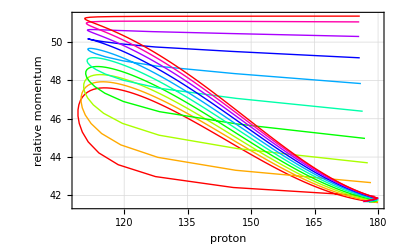

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,2.2, m11B, mp, md,mn,mp,200][[1;;7;;6]],{θk, 10, 100,10},{θc, 0, 178,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/9}], Frame->True,FrameLabel->{"proton","relative momentum"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

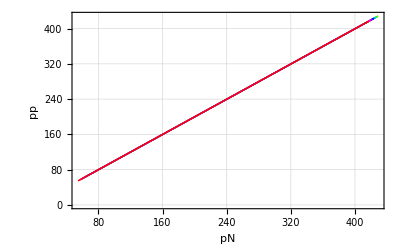

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,2.2, m10B, mp, md,mn,mp,200][[5;;6]],{θk, 0, 90,10},{θc, 0, 180,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/9}], Frame->True,FrameLabel->{"pN","pp"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

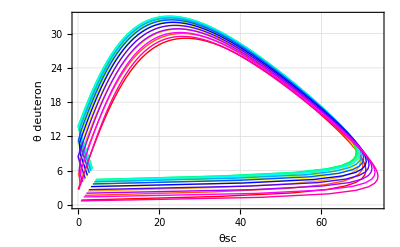

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,0, m11B, mp, mn+mp,mn,mp,200][[1;;2]],{θk, 10, 170,10},{θc,0,178,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/18}], Frame->True,FrameLabel->{"θsc","θ deuteron"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

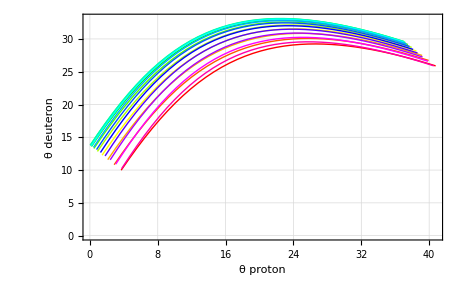

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,2.2, m12B, mp, md,mn,mp,200][[1;;2]],{θk, 10, 170,10},{θc,90,170,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/18}], Frame->True,FrameLabel->{"θ proton","θ deuteron"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

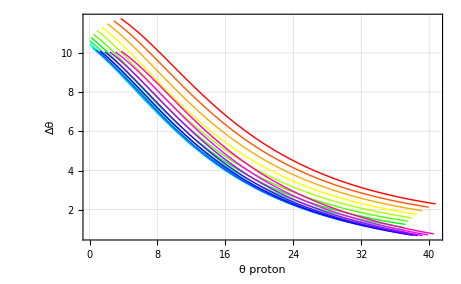

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,2.2, m12B, mp, md,mn,mp,200][[1;;3;;2]],{θk, 10, 170,10},{θc, 90, 170,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/18}], Frame->True,FrameLabel->{"θ proton","Δθ"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], PlotRange->All]
```

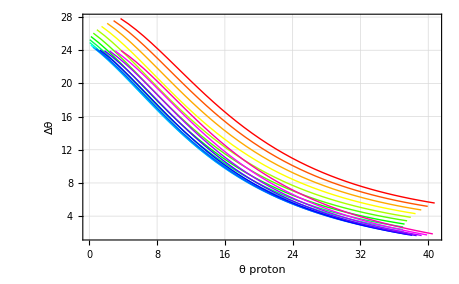

```mathematica
ListPlot[Table[knockout[100, θk °,0, θc °,0, 10,100,π/2,0,0, m12B, mp, mn+mp,mn,mp,200][[1;;3;;2]],{θk, 10, 170,10},{θc, 90, 170,2}], Joined->True, PlotStyle->Table[Hue[i],{i,0,1,1/18}], Frame->True,FrameLabel->{"θ proton","Δθ"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], PlotRange->All]
```

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θc °,ϕc °,S,kNN, θNN ° , ϕNN °, SNN, mTar,mInc,mKnock,m1, m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",
{"k",k,"θk, ϕk",θk ,ϕk  },
{"S",S,"θc, ϕc",θc ,ϕc },
{"kNN",kNN,"θNN, ϕNN",θNN ,ϕNN },
{"βPI",βPI},
{"Nucleus frame ", "----", "----", "----"},DisVector[PI,"PI"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-PI-Pn,"Diff"],
DisVector[P2a,"P2a"],DisVector[P2b,"P2b"],
{"angle diff",ΔAngle[P2a,P2b] 180/π},
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[PIc,"PIc"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],
Graphics[{
{Cyan,Arrow[{{-PIL[[2]],-PIL[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{P2aL[[2]],P2aL[[4]]}}]},
{Purple, Arrow[{{0,0},{P2bL[[2]],P2bL[[4]]}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab Frame",ImageSize->500],
{Graphics[{
{Cyan,Arrow[{{-PI[[2]],-PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{P2a[[2]],P2a[[4]]}}]},
{Purple, Arrow[{{0,0},{P2b[[2]],P2b[[4]]}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Nucleus",ImageSize->250]
,
Graphics[{
{Cyan,Arrow[{{-PIc[[2]],-PIc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[PIc,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]},ImageSize->250]
}
}
}]
,{{mInc,mp},{mp->"Proton",mn->"Neutron"}},{{mKnock,md},{mp+mp->"p-p",mn+mn->"n-n",mn+mp->"n-p",md->"deuteron"}},{{m1,mn},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron"}},{{mTar,m12B},massList},{{TiL,200},0,300},{{k,100},{0,50,100,150,200,270}},{{θk,90},0,180},{{ϕk,0},-180,180},{{S,10},{0,10, 14.43,20,30,41.53}},{{θc,90},0,180},{{ϕc,0},-180,180},{{kNN,100},0,100},{{θNN,90},-180,180},{{ϕNN,0},-180,180},{{SNN,2.2},{0, 2.2}},ControlPlacement->Left]
```

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θc °,ϕc °,S,kNN, θNN ° , ϕNN °, SNN, mTar,mInc,mKnock,m1, m2,TiL];
ListPlot[Table[],,Joined->True]
,{{mInc,mp},{mp->"Proton",mn->"Neutron"}},{{mKnock,md},{mp+mp->"p-p",mn+mn->"n-n",mn+mp->"n-p",md->"deuteron"}},{{m1,mn},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron"}},{{mTar,m10B},massList},{{TiL,200},0,300},{{k,100},{0,50,100,150,200,270}},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,0},{0, 14.43,20,30,41.53}},{{θc,90},-180,180},{{ϕc,0},-180,360},{{kNN,30},0,100},{{θNN,90},-180,180},{{ϕNN,0},-180,180},{{SNN,0},{0, 2.2}},ControlPlacement->Left]
```